```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/tools"];
```

## Cos temp profile setup

```mathematica
au=1.496*10^13;rc=115 au;rcInAu=115;
```

### Define reference parameters

```mathematica
Tatm0=40;
Tmid0=19;
zq0=2.0;
```

### Define how the parameters scale with r (relative to the reference parameters)

```mathematica
Tmid[r_]:=Tmid0(r/(200 au))^-0.5;
Tatm[r_]:=Tatm0(r/(155 au))^-0.3;
zq[r_]:=63au(r/(200 au))^1.3*Exp[-(r/(800au))^2];
δ[r_]:=0.0034(r/(1au)-200)+2.5;
```

### Define the temperature profile as a function of z in physical units

```mathematica
Tcos[r_,z_]:=If[Abs[z]<zq[r],Tatm[r]+(Tmid[r]-Tatm[r])(Cos[(π z)/(2zq[r])])^(2δ[r]),Tatm[r]];
```

### Convert the profile to physical units

```mathematica
kb=1.38*10^-16;mH=1.67372*10^-24;G=6.674*10^-8;Msun=1.988435*10^33;
Mstar=2.3*Msun;μ=2.37;
cs[r_]:=√((kb Tmid[r])/(μ mH))
Ω[r_]:=√((G Mstar)/r^3)
H[r_]:=(√2 cs[r])/Ω[r]
```

```mathematica
codeT=((Tmid[rc]+Tatm[rc])/2)/0.5;
```

```mathematica
TcosUnits[r_,z_]:=Tcos[r*au,z*H[r*au]]/codeT
```

```mathematica
P0=0.5;
sCos=NDSolve[{1/ρ1[z1] D[(TcosUnits[rcInAu,z1]*ρ1[z1]), z1]==-z1,ρ1[0]==P0/TcosUnits[rcInAu,0]},ρ1[z1],{z1,0,4}];
ρCos[z1_]:=Re[Evaluate[ρ1[z1]/.sCos]];
Pcos[z1_]:=ρCos[z1]*TcosUnits[rc,z1]
```

## AD setup

```mathematica
Plot[ρCos[rcInAu,z],{z,-4,4}]
```

-Graphics-

```mathematica
TcosUnits[rcInAu,0]*ρCos[0]
```

{0.364173 Re[ρ1[0]]}

```mathematica
Ω1=1;
Q=1;
βmid=10^5;
Bsq[z_]:=TcosUnits[rcInAu,0]*ρCos[z1]/βmid/.{z1->z}
β[z_]:=(TcosUnits[rcInAu,z1]*ρCos[z1])/Bsq[z1]/.{z1->z}
```

```mathematica
AmQd[z_,Q_,d_]:=ρCos[z1]^d/(Ω1 Q)/.{z1->z}
AmFlat[z_,η_]:=(TcosUnits[rcInAu,z1]/β[z1])/(η Q)/.{z1->z}
```

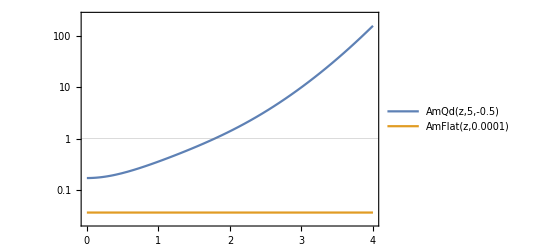

```mathematica
LogPlot[{AmQd[z,5,-0.5],AmFlat[z,0.0001]},{z,0,4},PlotRange->Full,PlotLegends->"Expressions",GridLines->{{},{1}},Frame->True]
```